# Introducción a Mathematica parte II

Autor: Wargner A. Moreno Losada
Departamento de Química
01 de Octubre de 2020

## Comandos * y . (Complemento operaciones con vectores y matrices)

El comando * se usa para realizar operaciones componente a componente, ya sean matrices o vectores:

Si A=(a_11 | a_12
a_21 | a_22) y B=(b_11 | b_12
b_21 | b_22)  entonces: A*B=B*A=(a_11 b_11 | a_12 b_12
a_21 b_21 | a_22 b_22) 

Si u=(u_1
u_2) y v=(v_1
v_2)  entonces u*v=v*u=(u_1 v_1
u_2 v_2)

Para realizar la multiplicación usual entre matrices:

AB=(a_11 | a_12
a_21 | a_22)(b_11 | b_12
b_21 | b_22)=(a_11 b_11+a_12 ab_21 | a_11 b_12+a_12 b_22
a_21 b_11+a_22 b_21 | a_21 b_12+a_22 b_22)

Se emplea el comando: A.B

Recuerde que el producto entre matrices no es conmutativo, luego A.B≠B.A

```mathematica
A={{Subscript[a, 11],Subscript[a, 12]},{Subscript[a, 21],Subscript[a, 22]}}; (*    Para escribir subindices en las variables use el comando "ctrl" + "_"    *)
```

```mathematica
B={{Subscript[b, 11],Subscript[b, 12]},{Subscript[b, 21],Subscript[b, 22]}};
```

```mathematica
A.B // MatrixForm (* Recuerde que este tipo de cálculos en Mathematica son posibles porque se puede trabajar a un nivel simbólico *)
```

(a_11 b_11+a_12 b_21 | a_11 b_12+a_12 b_22
a_21 b_11+a_22 b_21 | a_21 b_12+a_22 b_22)

```mathematica
B.A//MatrixForm
```

(a_11 b_11+a_21 b_12 | a_12 b_11+a_22 b_12
a_11 b_21+a_21 b_22 | a_12 b_21+a_22 b_22)

```mathematica
A*B//MatrixForm
```

(a_11 b_11 | a_12 b_12
a_21 b_21 | a_22 b_22)

## Comando Manipulate

El comando Manipulate [] sirve para controlar de forma discreta o continua parámetros en expresiones o gráficas.

```mathematica
(* Manipular polinomios *)
```

```mathematica
Manipulate[Expand[(1+x)^n],{n,1,6,1}]
```

```mathematica
(* Manipular gráficos *)
```

```mathematica
Manipulate[Plot[a*Sin[κ t],{t,0,2 Pi}],{κ,1,5},{a,2,10}]
```

```mathematica
Manipulate[Plot3D[Sin[a*x1+x2],{x1,0,2Pi},{x2,0,2Pi}],{a,0,20}]
```

## Series de potencias y sumas parciales

Mathematica tiene comandos especiales para encontrar la representación de una función en series de potencia (Taylor, Fourier, etc.) Sin embargo solo nos centraremos en la expansión en series de Taylor y el cálculo de sumas parciales para algunas series.

Nos centraremos en hallar la representación en series de Taylor para la función exponencial

ⅇ^x=1+x+1/(2!)x^2+1/(3!)x^3+1/(4!)x^4+....+1/(n!)x^n=∑_(i=1)^n x^i/(i!)

La cual truncaremos en la 4 potencia, compararemos la aproximación gráficamente para x = 3. Para esto usaremos el comando Series[f[x],{x,x0,número de términos}]

Posteriormente se calcularán algunas sumas parciales para la serie convergente:

∑_(k=1)^∞ 1/2^k=1

```mathematica
Series[Exp[x],{x,3,4}]
```

ⅇ^3+ⅇ^3 (x-3)+1/2 ⅇ^3 (x-3)^2+1/6 ⅇ^3 (x-3)^3+1/24 ⅇ^3 (x-3)^4+O[x-3]^5

```mathematica
Clear["x"]
```

```mathematica
fapprox[x_]:=ⅇ^3+ⅇ^3 (x-3)+1/2 ⅇ^3 (x-3)^2+1/6 ⅇ^3 (x-3)^3+1/24 ⅇ^3 (x-3)^4;
```

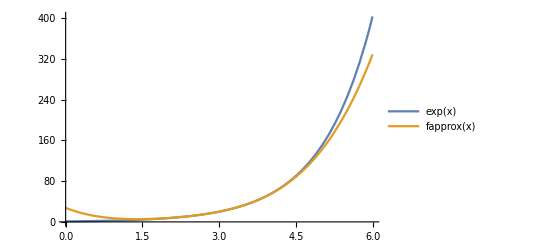

```mathematica
Plot[{Exp[x],fapprox[x]},{x,0,6},PlotLegends->"Expressions"]
```

```mathematica
fn[K_]:=∑_(j=1)^K (1./2)^j;
```

Sumas parciales de la serie anterior:

```mathematica
Table[{K,fn[K]},{K,1,30}]
```

{{1,0.5},{2,0.75},{3,0.875},{4,0.9375},{5,0.96875},{6,0.984375},{7,0.992188},{8,0.996094},{9,0.998047},{10,0.999023},{11,0.999512},{12,0.999756},{13,0.999878},{14,0.999939},{15,0.999969},{16,0.999985},{17,0.999992},{18,0.999996},{19,0.999998},{20,0.999999},{21,1.},{22,1.},{23,1.},{24,1.},{25,1.},{26,1.},{27,1.},{28,1.},{29,1.},{30,1.}}

## Coordenadas Polares

Para hacer un cambio de coordenadas cartesianas a coordenadas polares se emplea el siguiente comando: ToPolarCoordinates[{x,y}]
La gráfica de una función en coordenadas polares r = f(θ)se logra con ayuda del comando PolarPlot[r[θ],{θ,θ_min,θ_max}]

Ej.  convertir de las coordenadas cartesianas (0,1) a coordenadas polares.
       grafique la lemniscata r^2=3^2 cos(2θ)

```mathematica
ToPolarCoordinates[{0,1}]
```

{1,π/2}

```mathematica
Clear["t"]
```

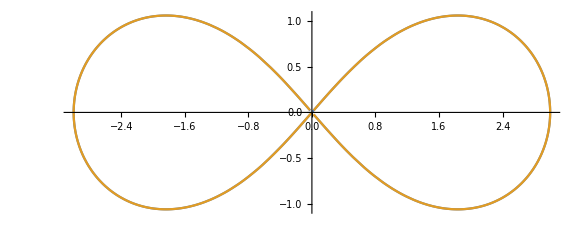

```mathematica
PolarPlot[{3 √Cos[2t],-3 √Cos[2t]},{t,0,2 Pi}]
```

## Derivadas e Integrales

Mathematica nos permite realizar derivación e integración en una y varias variables (sobre una diversidad de regiones en el plano y en el espacio), por ahora solo se presentará el caso de una variable real:

D[f[x],{x,orden de la derivada}] para encontrar derivadas
Integrate[] para integrar

Ejemplo: Hallar la cuarta derivada de la función: Cos[2 (x])^3
                    Calcule la integral definida para la función x^2 para x∈[0,1]
                    Calcule la integral indefinida para la función 1/x usando el ayudante de matemática básica.

```mathematica
D[Cos[2 x]^3,{x,4}] (* Puedo poner directamente la función o crearla a parte si la voy a utilizar en más cálculos*)
```

336 Cos[2 x]^3-960 Cos[2 x] Sin[2 x]^2

```mathematica
Integrate[x^2,{x,0,1}]
```

1/3

```mathematica
∫1/x ⅆx (* se puede escribir esc + intt + esc para escribir la integral, Mathematica omite la contante de integración para una integral indefinida*)
```

Log[x]

## Tarea

1) Diseñe una matriz simétrica de tamaño 8×8 usando el comando Table[] con la propiedad: a_ii>a_ij para j≠i. Compruebe que la matriz es simétrica usando el comando Transpose[] de forma que el resultado sea una variable booleana (es decir que tome valor verdadero “True”).  Halle el espacio nulo para la matriz anterior e interprete los resultados.
2) Realice la gráfica para la presión total de un sistema P_T vs la fracción molar del soluto. El sistema se compone de dos líquidos volátiles que satisfacen la ley de Raoult:
1.28 moles de A y  4.11 moles de B con presiones de vapor en su estado puro de P_A^0=300 mmHg, P_B^0=400 mmHg. En la gráfica la presión total debe aparecer con un trazo más grueso, y los presiones de vapor individuales con lineas punteadas, cada eje y cada curva debe tener su rótulo respectivo. [Ayuda: Explore las opciones del comando Plot]
3) Un sistema conformado por 3.01 moles de gas ideal realiza trabajo PV desde el punto A(3.00 L,8.00 atm) hasta el punto B(8.00 L,1.00 atm) los cuales están conectados por una trayectoria circular cuyo centro se encuentra en (3.00,1.00). Grafique el área bajo de la curva y calcule el trabajo hecho por el sistema respetando la convención de signos establecida en clase. [Ayuda: resuelva el problema usando coordenadas polares y cartesianas piense el área bajo la curva como dos regiones distintas para hacer esto, compare los resultados resolviendo la integral en coordenadas cartesianas]
4) Con ayuda del comando Manipulate[] ejecute un gráfico donde se presente la ley de Henry c =kP para diferentes valores de la constante de Henry. Busque 3-4 constantes diferentes en la literatura para incluir en el comando.
5) Exprese la presión de un gas ideal en función del volumen manteniendo constante los demás parámetros (n,T) y encuentre la segunda derivada. Haga lo mismo para el modelo de gases reales propuesto por Van der Waals. 
6) Explore el comando Norm[] para calcular la norma de un vector y haga la normalización de un vector cualquiera. (El comando tiene usos más generales para determinar la norma de vectores y matrices)

La solución a estos ejercicios se publicará el día Lunes 5 de Octubre en el campus virtual.